```mathematica
(*   Copyright: Pengcheng Xie, Connnect: xpc@lsec.cc.ac.cn    *)

ClearAll[answer]

(*Define constants*)
G=-1;
H=-2;
ω1=3;
ω2=3;
κ=-2;

(*Define a function to calculate the answer*)
answer[ε_,m_,ω1_,ω2_]:=Module[{ans},ans=Integrate[Boole[G+((1+κ) ω2 (H+ω3))/(H+H ε-κ ω1+ω3+ε ω3)+ω4>=0&&G+ω4<=((1+κ) ω2 (H+ω3))/(H (-1+ε)+κ ω1+(-1+ε) ω3)],{ω3,0,m ω1},{ω4,0,m ω2}];
ans/(m^2 ω1 ω2)]


answer1=answer[ε,10^(-3),ω1,ω2];
answer2=answer[ε,10^(-2),ω1,ω2];
answer3=answer[ε,10^(-1),ω1,ω2];
answer4=answer[ε,1,ω1,ω2];
answer5=answer[ε,10^(1),ω1,ω2];
answer6=answer[ε,10^(2),ω1,ω2];
answer7=answer[ε,10^(3),ω1,ω2];
answer8=answer[ε,10^(4),ω1,ω2];
```

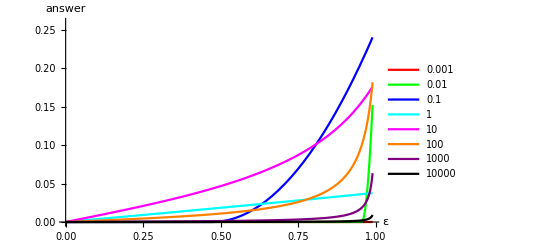

```mathematica
(*Plot the answers*)
Plot[{answer1,answer2,answer3,answer4,answer5,answer6,answer7,answer8},{ε,0,0.99},PlotStyle->{Red,Green,Blue,Cyan,Magenta,Orange,Purple,Black},PlotLegends->{"0.001","0.01","0.1","1","10","100","1000","10000"},AxesLabel->{"ε","answer"},PlotRange->{0,0.26}]
```

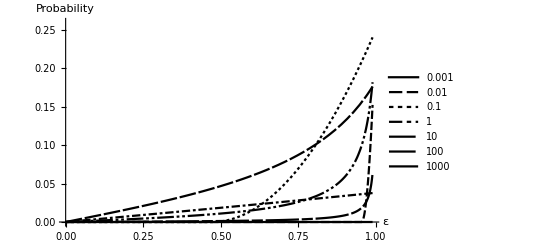

```mathematica
Plot[{answer1,answer2,answer3,answer4,answer5,answer6,answer7},{ε,0,0.99},PlotTheme->"Monochrome",PlotStyle->{GrayLevel[0]},PlotLegends->{"0.001","0.01","0.1","1","10","100","1000"},AxesLabel->{"ε","Probability"},PlotRange->{0,0.26},LabelStyle->{FontFamily->"Helvetica",FontSize->18}]
```

```mathematica
tu=Plot[{answer1,answer2,answer3,answer4,answer5,answer6,answer7},{ε,0,0.99},PlotTheme->"Monochrome",PlotStyle->{Black},PlotLegends->{"0.001","0.01","0.1","1","10","100","1000"},AxesLabel->{"ε","Probability"},PlotRange->{0,0.26},LabelStyle->{FontFamily->"Times New Roman",FontSize->14}]
```

-Graphics-

```mathematica
Export["myPlot.eps",tu];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["myPlot.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["myPlot.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["myPlot.eps"]]]
```

```mathematica
SystemOpen["myPlot.eps"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["myPlot.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["myPlot.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["myPlot.eps"]]]
```

```mathematica
(*Set plot style*)myStyle={Red,Green,Blue,Cyan,Magenta,Orange,Purple,Black};

(*Plot the answers*)
myPlot=Plot[{answer1,answer2,answer3,answer4,answer5,answer6,answer7,answer8},{ε,0,0.99},PlotStyle->myStyle,PlotLegends->Placed[LineLegend[myStyle,{"m = 1","m = 2","m = 3","m = 4","m = 5","m = 6","m = 7","m = 8"},LabelStyle->{FontFamily->"Helvetica",FontSize->14}],Right],AxesLabel->{Style["ε",FontFamily->"Helvetica",FontSize->16],Style["answer",FontFamily->"Helvetica",FontSize->16]},PlotRange->{{0,1},{0,0.26}},ImageSize->500,PlotTheme->"Detailed"];
```

```mathematica
{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[1,0,1],RGBColor[1,0.5,0],RGBColor[0.5,0,0.5],GrayLevel[0]}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0.5, 0, 0.5],GrayLevel[0]}

```mathematica
{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[1,0,1],RGBColor[1,0.5,0],RGBColor[0.5,0,0.5],GrayLevel[0]}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0.5, 0, 0.5],GrayLevel[0]}

```mathematica
{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[1,0,1],RGBColor[1,0.5,0],RGBColor[0.5,0,0.5],GrayLevel[0]}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0.5, 0, 0.5],GrayLevel[0]}